### Categorization

Tutorial

EcoEvo Package

EcoEvo`

EcoEvo/tutorial/LeslieMatrixModels

### Keywords

example

Details

# Matrix Population Models

Leslie and Lefkovitch matrix models are discrete-time models that allow discrete age- and stage-structure respectively.  They take the general form

```mathematica
Needs["EcoEvo`"];
```

Rather than defining each component manually, use MatrixToPopComponents which automates the task.  For a 2x2 matrix:

```mathematica
MatrixToPopComponents[A,n,2]
```

{Component[n[1]]→{Equation:>A⟦1,1⟧ n[1][t]+A⟦1,2⟧ n[2][t]},Component[n[2]]→{Equation:>A⟦2,1⟧ n[1][t]+A⟦2,2⟧ n[2][t]}}

```mathematica
SetModel[{ModelType->"DiscreteTime",Pop[pop]->MatrixToPopComponents[A,n,2]}]
```

Define a Leslie matrix:

```mathematica
A={{3,8},{1/2,0}};
```

Simulate dynamics for 8 time steps:

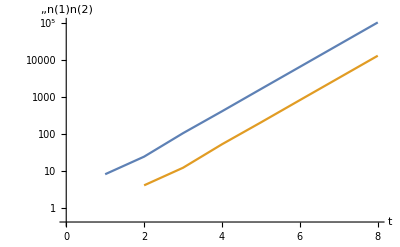

```mathematica
sol=EcoSim[{n[1]->0,n[2]->1},8];
PlotDynamics[sol,Logged->True]
```

Plot the ratio of population in age-1 to age-2:

Power::infy: Infinite expression 1/0 encountered.

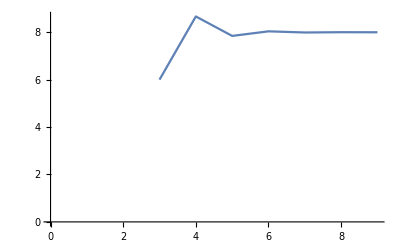

```mathematica
ListPlot[Table[n[1][t]/n[2][t]/.sol,{t,0,8}],Joined->True]
```

Together, we see that the population grows exponentially after it reaches a stable age distribution.  The growth rate is given by the dominant eigenvalue of the matrix:

```mathematica
Eigenvalues[A]
```

{4,-1}

which are the same as the eco-eigenvalues of the {n[1]→0,n[2]→0} equilibrium:

```mathematica
EcoEigenvalues[]
```

{4,-1}

and the same as the exponential of the invasion rate given by Inv:

```mathematica
E^Inv[]
```

4

The (right) eigenvector gives the stable age distribution

```mathematica
Eigenvectors[A]
```

{{8,1},{-2,1}}

which is the same as given by StablePopulationStructure:

```mathematica
StablePopulationStructure[]
```

{n[1]→8,n[2]→1}

Reproductive values are given by the left eigenvector, obtained from the transpose of A:

```mathematica
Eigenvectors[Transpose[A]]
```

{{1/2,1},{-1/8,1}}

which can be obtained from ReproductiveValues.

```mathematica
ReproductiveValues[]
```

{n[1]→1,n[2]→2}

### References

Caswell, H. 2000. Matrix Population Models: Construction, Analysis, and Interpretation, 2nd ed. Sinauer.

Leslie, P.H. 1945. On the use of matrices in certain population mathematics. Biometrika 33: 213–245.

More About

Related Tutorials

ExampleModels

Related Wolfram Education Group Courses